```mathematica
Quit[]
```

```mathematica
Needs@"RunningCouplings`"
```

```mathematica
?"RunningCouplings`*"
```

```mathematica
RunningCouplings[
"MSSM",
10^7,
"TanBeta"->10,
"LightestNeutrinoMass"->10^-12,
"NeutrinoMassHierarchy"->"Normal",
"NeutrinoMassOperator"->"Dirac",
"SupersymmetryScale"->10^4
]
```

<|RenormalizationScheme→DRbar,RenormalizationScale→10000000,g1→0.5080.0040.004,g2→0.64050.00130.0014,g3→0.8590.0080.008,yu→4.520.080.0910^-6,yc→0.002170.000040.00004,yt→0.6960.0140.014,yd→0.00009222222,ys→0.001840.000040.00004,yb→0.09730.00210.0021,ye→0.000110899,ymu→0.005640.000050.00005,ytau→0.09600.00080.0008,y1→6.0370.0120.01110^-15,y2→5.230.220.2110^-14,y3→3.040.060.0610^-13,CKM→<|Parametrization→Wolfenstein,Lambda→0.236170.000210.0012,A→0.7850.040.015,RhoBar→0.2140.0170.030,EtaBar→0.2940.0210.024,JarlskogInvariant→0.00003143830|>,PMNS→<|Parametrization→Standard,Theta12→0.590.040.04,Theta23→0.850.130.05,Theta13→0.1500.0070.007,Delta→3.91.32.4,JarlskogInvariant→-0.02210.00120.05|>|>

```mathematica
RunningGaugeCoupling[
{"MSSM", 3},
10^12,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]
```

0.749010.000120.00012

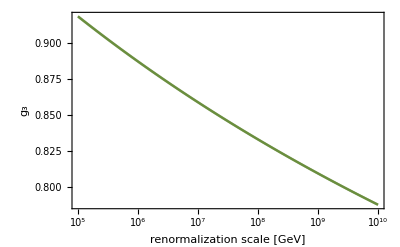

```mathematica
LogLinearPlot[
{
RunningGaugeCoupling[{"MSSM",3},scale]["Value"],
RunningGaugeCoupling[{"MSSM",3},scale]["Interval"]//Min,
RunningGaugeCoupling[{"MSSM",3},scale]["Interval"]//Max
},
{scale,10^5,10^10},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","g_3"},
PlotStyle->{
Directive[ColorData["DarkRainbow"][0.4]],
Directive[ColorData["DarkRainbow"][0.4],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0.4],Opacity@0.5]
}
]
```

```mathematica
RunningYukawaCoupling[
{"MSSM","U",3},
10^12.5,
"TanBeta"->50,
"SupersymmetryScale"->10^4
]
```

0.5880.0080.008

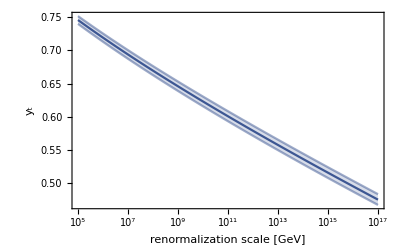

```mathematica
LogLinearPlot[
{
RunningYukawaCoupling[
{"MSSM","U",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Value"],
RunningYukawaCoupling[
{"MSSM","U",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Interval"]//Min,
RunningYukawaCoupling[
{"MSSM","U",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Interval"]//Max
},
{scale,10^5,10^17},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","y_t"},
PlotStyle->{
Directive[ColorData["DarkRainbow"][0]],
Directive[ColorData["DarkRainbow"][0],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0],Opacity@0.5]
}
]
```

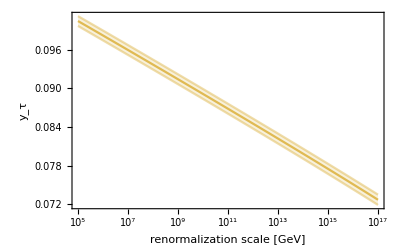

```mathematica
LogLinearPlot[
{
RunningYukawaCoupling[
{"MSSM","E",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Value"],
RunningYukawaCoupling[
{"MSSM","E",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Interval"]//Min,
RunningYukawaCoupling[
{"MSSM","E",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Interval"]//Max
},
{scale,10^5,10^17},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","y_τ"},
PlotStyle->{
Directive[ColorData["DarkRainbow"][0.7]],
Directive[ColorData["DarkRainbow"][0.7],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0.7],Opacity@0.5]
}
]
```

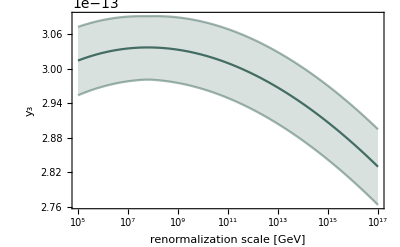

```mathematica
LogLinearPlot[
{
RunningYukawaCoupling[
{"MSSM","V",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Value"],
RunningYukawaCoupling[
{"MSSM","V",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Interval"]//Min,
RunningYukawaCoupling[
{"MSSM","V",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Interval"]//Max
},
{scale,10^5,10^17},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","y_3"},
PlotStyle->{
Directive[ColorData["DarkRainbow"][0.2]],
Directive[ColorData["DarkRainbow"][0.2],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0.2],Opacity@0.5]
}
]
```

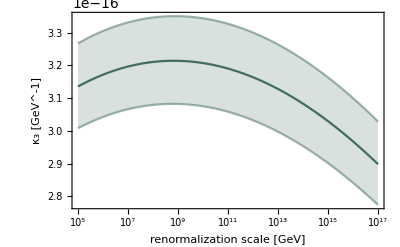

```mathematica
LogLinearPlot[
{
RunningWeinbergOperator[
{"MSSM",2},
scale,
"TanBeta"->50,
"SupersymmetryScale"->10^4
]["Value"],
RunningWeinbergOperator[
{"MSSM",2},
scale,
"TanBeta"->50,
"SupersymmetryScale"->10^4
]["Interval"]//Min,
RunningWeinbergOperator[
{"MSSM",2},
scale,
"TanBeta"->50,
"SupersymmetryScale"->10^4
]["Interval"]//Max
},
{scale,10^5,10^17},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","κ_3 [GeV^-1]"},
PlotStyle->{
Directive[ColorData["DarkRainbow"][0.2]],
Directive[ColorData["DarkRainbow"][0.2],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0.2],Opacity@0.5]
}
]
```

```mathematica
RunningMixingParameter[
{"MSSM","CKM","A"},
10^16,
"SupersymmetryScale"->10^4
]
```

0.6460.0310.012

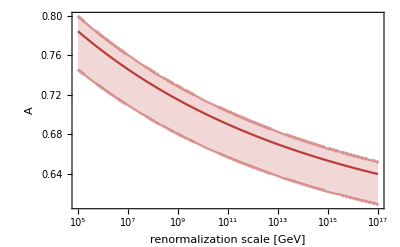

```mathematica
LogLinearPlot[
{
RunningMixingParameter[
{"MSSM","CKM","A"},
scale,
"SupersymmetryScale"->10^4
]["Value"],
RunningMixingParameter[
{"MSSM","CKM","A"},
scale,
"SupersymmetryScale"->10^4
]["Interval"]//Min,
RunningMixingParameter[
{"MSSM","CKM","A"},
scale,
"SupersymmetryScale"->10^4
]["Interval"]//Max
},
{scale,10^5,10^17},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","A"},
PlotRange->All,
PlotStyle->{
Directive[ColorData["DarkRainbow"][0.9]],
Directive[ColorData["DarkRainbow"][0.9],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0.9],Opacity@0.5]
}
]
```

```mathematica
RunningMixingParameter[
{"MSSM","PMNS","Theta12"},
10^16,
"TanBeta"->50,
"SupersymmetryScale"->10^4
]
```

0.570.040.04

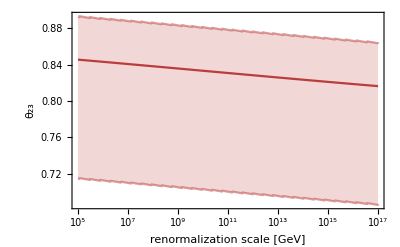

```mathematica
LogLinearPlot[
{
RunningMixingParameter[
{"MSSM","PMNS","Theta23"},
scale,
"TanBeta"->50,
"SupersymmetryScale"->10^4,
"LightestNeutrinoMass"->10^-12
]["Value"],
RunningMixingParameter[
{"MSSM","PMNS","Theta23"},
scale,
"TanBeta"->50,
"SupersymmetryScale"->10^4,
"LightestNeutrinoMass"->10^-12
]["Interval"]//Min,
RunningMixingParameter[
{"MSSM","PMNS","Theta23"},
scale,
"TanBeta"->50,
"SupersymmetryScale"->10^4,
"LightestNeutrinoMass"->10^-12
]["Interval"]//Max
},
{scale,10^5,10^17},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","θ_23"},
PlotRange->All,
PlotStyle->{
Directive[ColorData["DarkRainbow"][0.9]],
Directive[ColorData["DarkRainbow"][0.9],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0.9],Opacity@0.5]
}
]
```